```mathematica
ClearAll["Global`*"]
```

```mathematica
Needs["NumericalCalculus`"]
```

### Task & Variables

Analyze dispersion in a fiber waveguide with W-profile refraction index

```mathematica
a1=1.35×10^-6;
a2=4×10^-6;
dn1=25×10^-3;
dn2=10×10^-3;
(*λ=1500×10^-9;*)
m=0;
n=0;
c=3×10^8;
λ[ω_]:=(2×π×c)/ω;
(*k0=(2×π)/λ;*)
```

Calculating material dispersion according to Selmeier’s formula

```mathematica
as1=0.69616630;
as2=0.40794260;
as3=0.89747940;
ls1=0.0684043×10^-6;
ls2=0.11624140×10^-6;
ls3=9.8961610×10^-6;
nclad2[ω_]:=Sqrt[1+(as1×λ[ω]^2)/(λ[ω]^2-(ls1)^2)+(as2×λ[ω]^2)/(λ[ω]^2-(ls2)^2)+(as3×λ[ω]^2)/(λ[ω]^2-(ls3)^2)];
nclad1[ω_]:=nclad2[ω]-dn2;
ncore[ω_]:=nclad2[ω]+dn1;
```

### Calculations

```mathematica
k0[ω_]:=(2×π)/λ[ω];
u[neff_,ω_,r_]:=r×k0[ω]×√(ncore[ω]^2-neff^2);
w[neff_,ω_,r_]:=r×k0[ω]×√(neff^2-nclad1[ω]^2);
v[neff_,ω_,r_]:=r×k0[ω]×√(neff^2-nclad2[ω]^2);
```

```mathematica
NEff[ω_]:=neff/.FindRoot[Det[
{{BesselJ[m,u[neff,ω,a1]],-BesselK[m,w[neff,ω,a1]],-BesselI[m,w[neff,ω,a1]],0},
{u[neff,ω,a1]×1/2(BesselJ[m-1,u[neff,ω,a1]]-BesselJ[m+1,u[neff,ω,a1]]),-w[neff,ω,a1]×1/2(-BesselK[m-1,w[neff,ω,a1]]-BesselK[m+1,w[neff,ω,a1]]),-w[neff,ω,a1]×1/2(BesselI[m-1,w[neff,ω,a1]]+BesselI[m+1,w[neff,ω,a1]]),0},
{0,BesselK[m,w[neff,ω,a2]],BesselI[m,w[neff,ω,a2]],-BesselK[m,v[neff,ω,a2]]},{0,w[neff,ω,a2]×1/2(-BesselK[m-1,w[neff,ω,a2]]-BesselK[m+1,w[neff,ω,a2]]),w[neff,ω,a2]×1/2(BesselI[m-1,w[neff,ω,a2]]+BesselI[m+1,w[neff,ω,a2]]),-v[neff,ω,a2]×1/2(-BesselK[m-1,v[neff,ω,a2]]-BesselK[m+1,v[neff,ω,a2]])}}]==0,{neff,ncore[ω]-10^-9}]
```

```mathematica
NEff[1.5×10^15]
```

1.45375

```mathematica
coeffs[ω_]:=Solve[BesselJ[m,u[NEff[ω],ω,a1]]==b×BesselK[m,w[NEff[ω],ω,a1]]+cc×BesselI[m,w[NEff[ω],ω,a1]]&&b×BesselK[m,w[NEff[ω],ω,a2]]+cc×BesselI[m,w[NEff[ω],ω,a2]]==d×BesselK[m,v[NEff[ω],ω,a2]]&&u[NEff[ω],ω,a1]×(BesselJ[m-1,u[NEff[ω],ω,a1]]-m/u[NEff[ω],ω,a1]×BesselJ[m,u[NEff[ω],ω,a1]])==b×w[NEff[ω],ω,a1]×(-BesselK[m-1,w[NEff[ω],ω,a1]]-m/w[NEff[ω],ω,a1]×BesselK[m,w[NEff[ω],ω,a1]])+cc×w[NEff[ω],ω,a1]×(BesselI[m-1,w[NEff[ω],ω,a1]]-m/w[NEff[ω],ω,a1]×BesselI[m,w[NEff[ω],ω,a1]]),{b,cc,d}];
```

```mathematica
BB[ω_]:=b/.coeffs[ω][[1,1]];
CC[ω_]:=cc/.coeffs[ω][[1,2]];
DD[ω_]:=d/.coeffs[ω][[1,3]];
```

```mathematica
R[ω_,r_]:=Piecewise[{{BesselJ[m,u[NEff[ω],ω,r]],r<=a1},{BB[ω]×BesselK[m,w[NEff[ω],ω,r]]+CC[ω]×BesselI[m,w[NEff[ω],ω,r]],a1<r<a2},{DD[ω]×BesselK[m,v[NEff[ω],ω,r]],r>=a2}}];
```

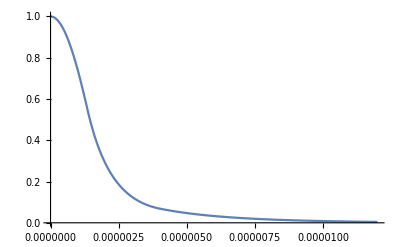

```mathematica
Plot[R[(2×π×c)/(1.55×10^-6),r],{r,0,3×a2},PlotRange->All]
```

```mathematica
Plot[NEff[ω],{ω,(2×π×c)/(1.7×10^-6),(2×π×c)/(1.0×10^-6)},AxesLabel->{"Frequency [Hz]","n_eff"},ImageSize->Large]
```

-Graphics-

```mathematica
NEff[(2×π×c)/(1.2×10^-6)]×k0[(2×π×c)/(1.2×10^-6)]
```

7.62048×10^6

```mathematica
NEff[1.8×10^15]
```

1.46001

```mathematica
(*Export["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 5\\NEff.dat",Table[{ω,NEff[ω]},{ω,1.1×10^15,1.885×10^15,10^12}]];*)
```

```mathematica
βtab=Table[{ω,NEff[ω]×k0[ω]},{ω,1.1×10^15,1.885×10^15,10^13}];
```

```mathematica
βfit[ω_]=Fit[βtab,{1,ω,ω^2,ω^3,ω^4},ω];
```

```mathematica
βfit[1.2×10^15]
```

5.78073×10^6-8.12768×10^-12 ⅈ

```mathematica
β2=Table[0,{i,Length[βtab]},{j,2}];
For[i=1,i≤Length[β2],i++,β2[[i,1]]=λ[βtab[[i,1]]]];
For[i=3,i<Length[β2]-1,i++,β2[[i,2]]=((-βtab[[i+2,2]]+16βtab[[i+1,2]]-30×βtab[[i,2]]+16βtab[[i-1,2]]-βtab[[i-2,2]])/(12×(βtab[[2,1]]-βtab[[1,1]])^2))×10^27];
```

```mathematica
(*β2fit=Table[0,{i,Length[βtab]},{j,2}];
For[i=1,i≤Length[β2],i++,β2fit[[i,1]]=λ[βtab[[i,1]]]];
For[i=1,i<Length[β2],i++,β2fit[[i,2]]=ND[βfit[ω],{ω,2},βtab[[i,1]],WorkingPrecision->10^7]×10^27];*)
```

```mathematica
ListPlot[βtab]
```

-Graphics-

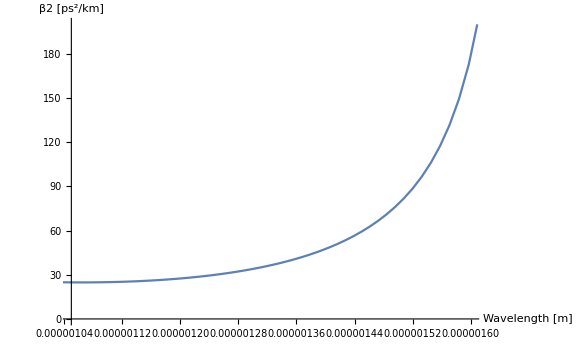

```mathematica
ListLinePlot[β2,PlotRange->{{1.05×10^-6,1.6×10^-6},{0,200}},AxesLabel->{"Wavelength [m]","β2 [ps^2/km]"},ImageSize->Large]
```

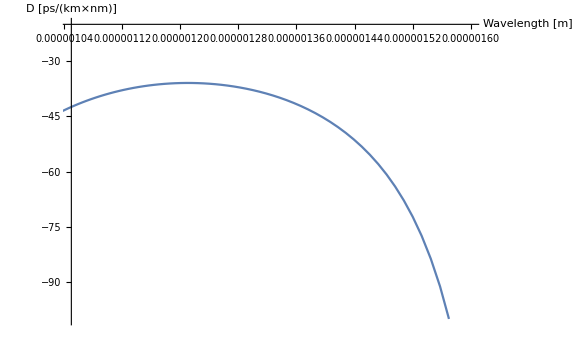

```mathematica
(*Disp[ω_]=-ω^2/(2×π×c)×β2[ω];*)
Disp=Table[0,{i,Length[βtab]},{j,2}];
For[i=1,i≤Length[Disp],i++,Disp[[i,1]]=λ[βtab[[i,1]]]];
For[i=3,i<Length[Disp]-1,i++,Disp[[i,2]]=(-2×π×c)/Disp[[i,1]]^2×β2[[i,2]]×10^6/10^27];
ListLinePlot[Disp,PlotRange->{{1.05×10^-6,1.6×10^-6},{-100,-20}},AxesLabel->{"Wavelength [m]","D [ps/(km×nm)]"},ImageSize->Large]
```